# Dünne Linsen

## Funktionen

```mathematica
GError[a_,b_,c_]:= (Total[Map[Abs,MapThread[D,{Table[a,{i,1,Length[b]}],b}]]*c]);
```

### Bessel

```mathematica
fBessel[va_,dva_,ve_,dve_] := Module[{a,e,da,de,f,fe},
f=1/4((a^2-e^2)/a);
fe= GError[f,{a,e},{da,de}];
{f,fe}/.{a->va,e->ve,da->dva,de->dve}]
```

## Laplace

### Berechnung

```mathematica
b = {{1, 1, 1, 1, 1, 1, 1, 1, 1, 1}};
g = {{8, 7, 6, 5, 4, 3, 3, 2, 2, 1}};
f = 1/(1/b+1/g)//N;
Grid[{b[[1]],g[[1]],f[[1]]},Frame->All]
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
8 | 7 | 6 | 5 | 4 | 3 | 3 | 2 | 2 | 1
0.888889 | 0.875 | 0.857143 | 0.833333 | 0.8 | 0.75 | 0.75 | 0.666667 | 0.666667 | 0.5

### Graph

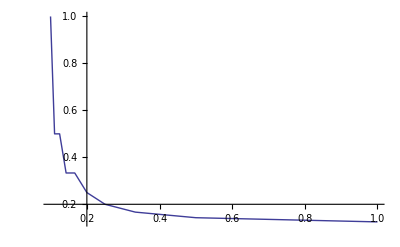

```mathematica
ListLinePlot[Table[{1/b[[1,x]],1/g[[1,x]]},{x,1,Length[b[[1]]]}]]
```

## Bessel Verfahren

### Messung

```mathematica
a2={1,2,3,4,5};
da2=0.1;
e2={1,1.4,1.5,1.7,1.8};
de2=0.2;
f2=Grid[fBessel[a2,da2,e2,de2],Frame->All]
```

0 | 0.255 | 0.5625 | 0.819375 | 1.088
0.15 | 0.10725 | 0.08125 | 0.0720156 | 0.06424

## Zerstreuungslinse

### Methode 1 : ohne/mit Zerstreuung

bo3 ist Abstand von der Sammellinse zum Bild ohne Zerstreuungslinse
bm3 ist der Abstand von der Sammellinse zum Bild mit Zerstreuungslinse
lsz3 ist der Abstand der Linsen
gsz3 ist der Gegenstandsabstand für die Zerstreuungslinse

```mathematica
bo3= {2,2,2,2,2,2,2,2,2,2};
bm3={3,3,3,3,3,3,3,3,3,3};
lsz3={1,1,1,1,1,1,1,1,1,1};
gz3 = bo3-lsz3
bz3 = bm3 -lsz3
f3 = 1/(1/-gz3+1/bz3)
```

{1,1,1,1,1,1,1,1,1,1}

{2,2,2,2,2,2,2,2,2,2}

{-2,-2,-2,-2,-2,-2,-2,-2,-2,-2}

### Methode 2 : ?